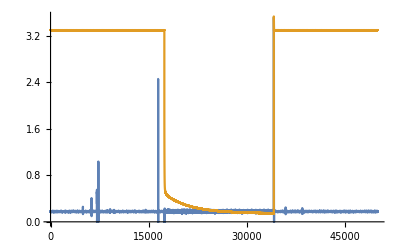

```mathematica
data=Import[NotebookDirectory[]<>"data0002.csv","List"];
tmp=Partition[data,Length[data]/2];
ai0=tmp[[1]];
ai1=tmp[[2]];
Clear[tmp];
ListPlot[{ai0,ai1},Joined->True,PlotRange->All]
hist=Import[NotebookDirectory[]<>"output.csv"];
(*hist=Import["C:\\Users\\weixu\\Google Drive\\claritypy\\clarity-plantower\\hist.csv","List"];*)
```

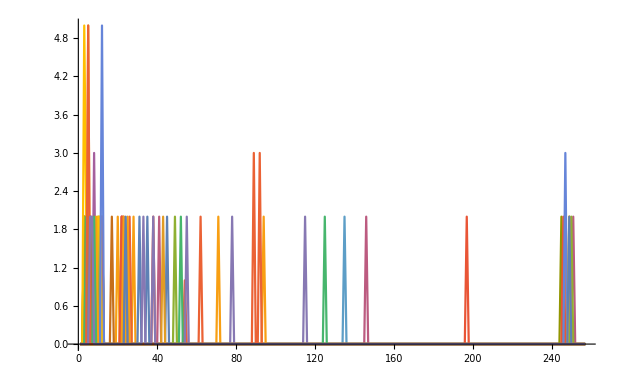

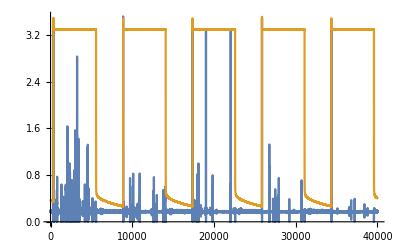

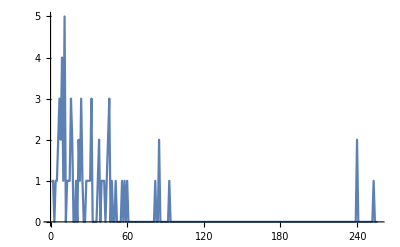

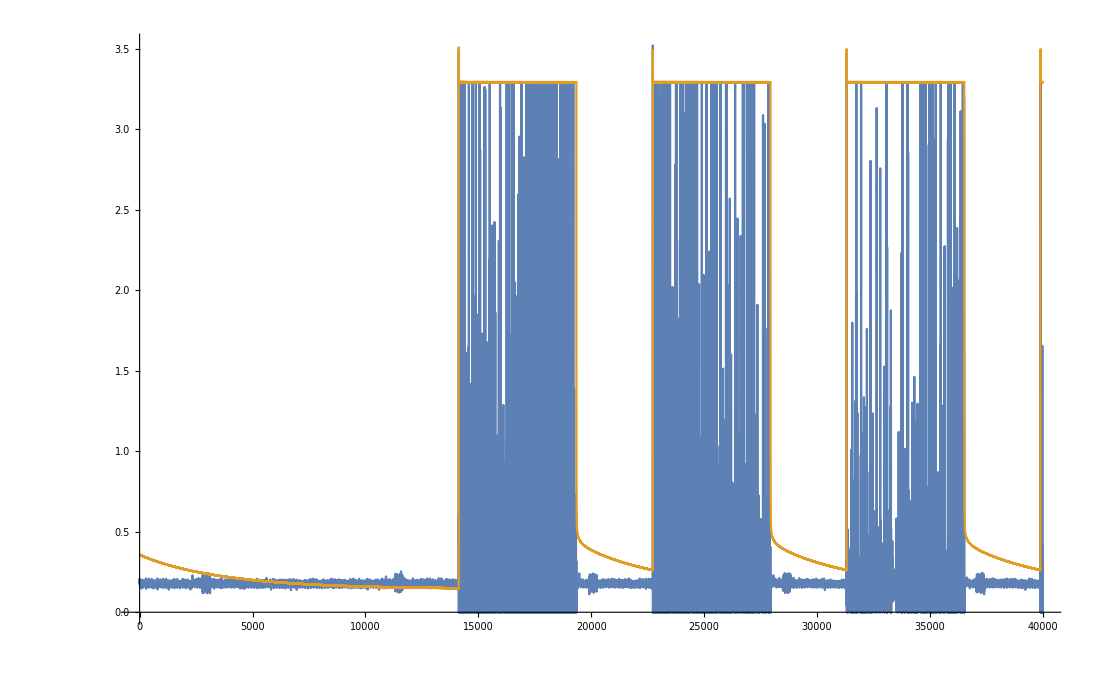

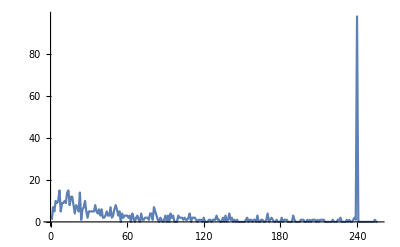

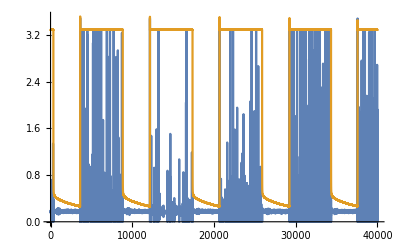

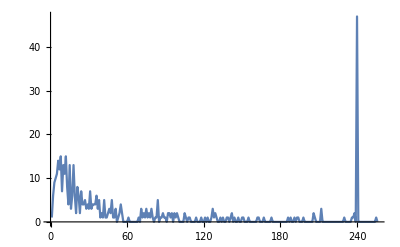

```mathematica
ListPlot[Drop[#,4]&/@Drop[hist,1],Joined->True]
```

```mathematica
x=Select[Abs[Drop[ai0,1]-Drop[ai0,-1]],#>0&];
Min[x]
Chop[x/Min[x]]
```

```mathematica
0.0003220624930690974.262
```

0.0000843804

```mathematica
Min[x]*2^16
```

21.1066875457764